```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Bf={125.295,121.724,126.464,132.312,135.328};
AT={34.03,33.20,34.3,35.638,36.32};
EB={290,710,200,30,24};
EBerr={{290,20},{710,40},{200,20},{32,2},{24,5}};
DataErr=Sort[Table[{{Bf[[i]],-EBerr[[i,1]]},ErrorBar[EBerr[[i,2]]]},{i,1,Dimensions[Bf][[1]]}]]
DataErr2=Table[{Bf[[i]],-EBerr[[i,1]],EBerr[[i,2]]},{i,1,Dimensions[Bf][[1]]}];
DataErrGraphics=DataErr2/.{x_,y_,e_}->{{PointSize[0.02],Point[{x,y}]},{Thickness[0.005],Line[{{x,y-e},{x,y+e}}]}};
```

{{{121.724,-710},ErrorBar[40]},{{125.295,-290},ErrorBar[20]},{{126.464,-200},ErrorBar[20]},{{132.312,-32},ErrorBar[2]},{{135.328,-24},ErrorBar[5]}}

```mathematica
ErrorListPlot[DataErr,Frame->True,PlotStyle->PointSize[0.02],PlotRange->{{121,140},{0,-800}},FrameLabel->{Binding energy (kHz),B field (G)}];
```

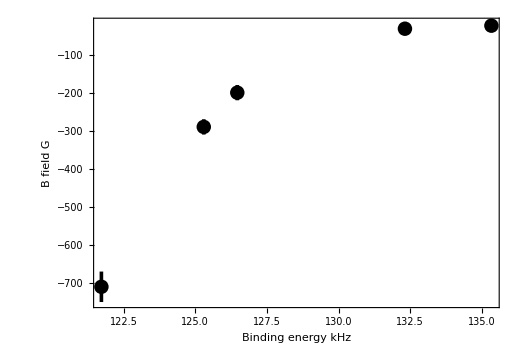

```mathematica
Show[Graphics[DataErrGraphics],Frame->True,AspectRatio->0.7,FrameLabel->{Binding energy (kHz),B field (G)}]
```

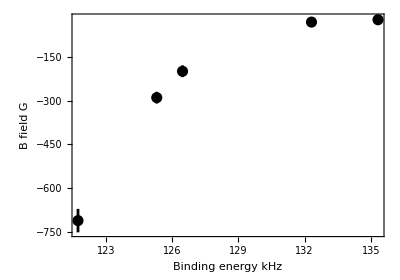

```mathematica
Show[Graphics[DataErrGraphics],Frame->True,AspectRatio->0.7,FrameLabel->{Binding energy (kHz),B field (G)},PlotRange->{{120,150},{0,-1000}}]
```